```mathematica
B[m_,n_,p_]:=Module[{},
If[Mod[m+n+p,2]>0,0,
Sqrt[m!n!/(Pi^(7/2)p!)]/2^((p+1) /2)
Sum[Binomial[p,k]Gamma[-k+1/2 (1+m+n+p-2 t)]Gamma[k-p+1/2 (1+m+n+p-2 t)]Gamma[-m-n+1/2 (1+m+n+p-2 t)+2 t]/(t!(m-t)!(n-t)!),{k,0,p},{t,0,Min[m,n]}]]
];
```

```mathematica
Mx=64;
Table[
ListDensityPlot[Table[B[m,n,p],{m,0,Mx-1},{n,0,Mx-1}]/N[B[0,0,0]],PlotRange->All,InterpolationOrder->0,ColorFunction-> "TemperatureMap"],{p,0,6}]
```

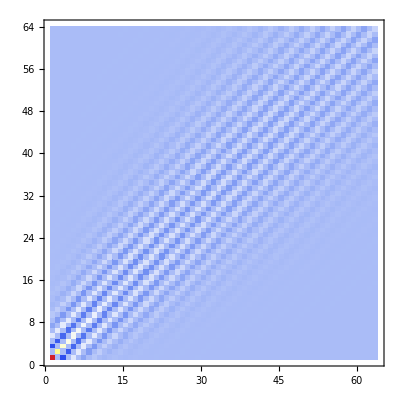
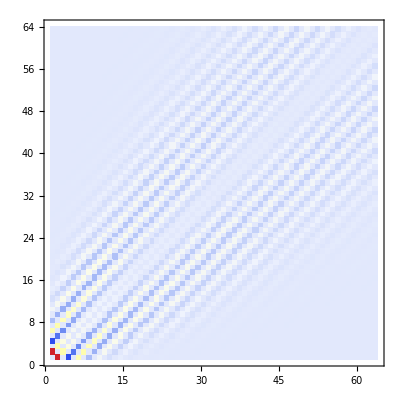
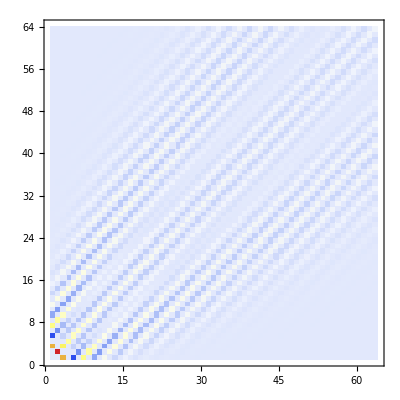
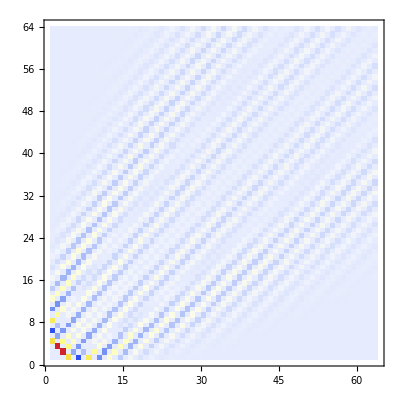
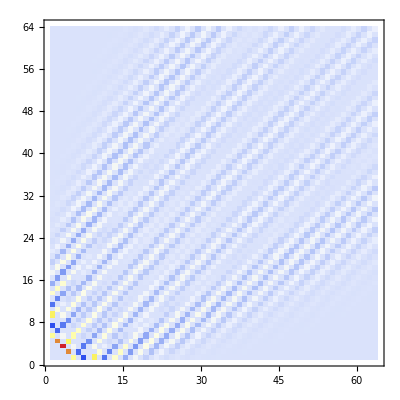
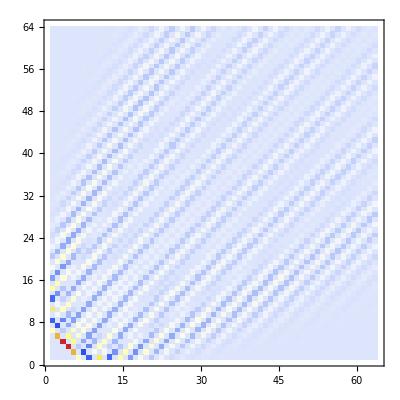
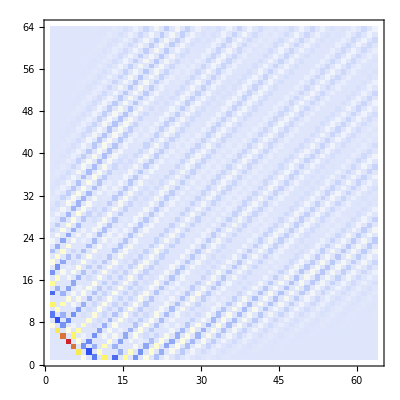

```mathematica
%23//MatrixForm
```

```mathematica
N[B[0,0,0]]
```

0.531126